```mathematica
f[t_]:=Exp[I  t] Sinh[ωt]
```

```mathematica
g[t_]:=Exp[I  t] Cos[ t]
```

```mathematica
Limit[f[t]-f[-t],t->Infinity]
```

ⅇ^(2 ⅈ Interval[{0,π}]) (-1+ⅇ^(2 ⅈ Interval[{0,π}])) Sinh[ωt]

```mathematica
Limit[g[t]-g[-t],t->Infinity]
```

ⅈ Interval[{-1,1}]

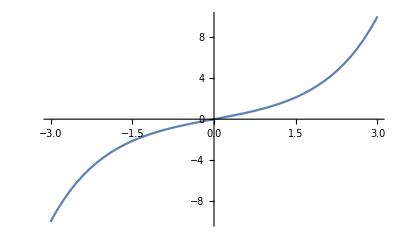

```mathematica
Plot[Sinh[x],{x,-3,3}]
```

```mathematica
?Assuming
```

RowBox[{"Assuming", "[", RowBox[{StyleBox["assum", "TI"], ",", StyleBox["expr", "TI"]}], "]"}] evaluates StyleBox["expr", "TI"] with StyleBox["assum", "TI"] appended to $Assumptions, so that StyleBox["assum", "TI"] is included in the default assumptions used by functions such as Refine, Simplify, and Integrate.

```mathematica
Assuming[{Element[nu,Reals],Element[omega,Reals]},Integrate[Exp[I nu tau]Exp[omega tau],{tau,0,Infinity}]]
```

ConditionalExpression[-1/(ⅈ nu+omega),omega<0]

```mathematica
xp=1/(ek+I omegan)/(I nun+ep-ek)
```

1/((-ek+ep+ⅈ nun) (ek+ⅈ omegan))

```mathematica
xm=1/(ek-I omegan)/(I nun+ep-ek)
```

1/((-ek+ep+ⅈ nun) (ek-ⅈ omegan))

```mathematica
Residue[xp,{ek,-I omegan}]
```

1/(ep+ⅈ nun+ⅈ omegan)

```mathematica
Residue[xm,{ek,I omegan}]
```

1/(ep+ⅈ nun-ⅈ omegan)

```mathematica
Residue[xp,{ek,ep+I nun}]
```

1/(-ep-ⅈ nun-ⅈ omegan)

```mathematica
Residue[xm,{ek,ep+I nun}]
```

1/(-ep-ⅈ nun+ⅈ omegan)

```mathematica
yp=1/(ep+I omegan)/(I nun+ep-ek)
```

1/((-ek+ep+ⅈ nun) (ep+ⅈ omegan))

```mathematica
ym=1/(ep-I omegan)/(I nun+ep-ek)
```

1/((-ek+ep+ⅈ nun) (ep-ⅈ omegan))

```mathematica
Residue[yp,{ek,-I omegan}]
```

0

```mathematica
Residue[ym,{ek,I omegan}]
```

0

```mathematica
Residue[yp,{ek,ep+I nun}]
```

1/(-ep-ⅈ omegan)

```mathematica
Residue[ym,{ek,ep+I nun}]
```

1/(-ep+ⅈ omegan)